# Pulsar radiation—Timing residual and pulse width

## Phase modulation and timing residuals

```mathematica
R=EulerMatrix[{ϕ,θ,ψ},{3,1,3}]
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],Cos[ψ] Sin[θ],Cos[θ]}}

```mathematica
m={Sin[χ],0,Cos[χ]}
```

{Sin[χ],0,Cos[χ]}

```mathematica
m1=R. m
```

{Cos[χ] Sin[θ] Sin[ϕ]+Sin[χ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]),-Cos[ϕ] Cos[χ] Sin[θ]+Sin[χ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]),Cos[θ] Cos[χ]+Sin[θ] Sin[χ] Sin[ψ]}

```mathematica
mx=m1[[1,;;]]
my=m1[[2,;;]]
```

Cos[χ] Sin[θ] Sin[ϕ]+Sin[χ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ])

-Cos[ϕ] Cos[χ] Sin[θ]+Sin[χ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])

```mathematica
my/mx
```

(-Cos[ϕ] Cos[χ] Sin[θ]+Sin[χ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]))/(Cos[χ] Sin[θ] Sin[ϕ]+Sin[χ] (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]))

```mathematica
Simplify[D[ArcTan[((Cos[ψ[t]]Sin[χ])/(Sin[θ]Cos[χ]-Cos[θ]Sin[ψ[t]]Sin[χ]))],{t,1}]]
```

(Sin[χ] (Cos[θ] Sin[χ]-Cos[χ] Sin[θ] Sin[ψ[t]]) ψ'[t])/(Cos[χ]^2 Sin[θ]^2-2 Cos[θ] Cos[χ] Sin[θ] Sin[χ] Sin[ψ[t]]+Sin[χ]^2 (Cos[ψ[t]]^2+Cos[θ]^2 Sin[ψ[t]]^2))

```mathematica
a2=Simplify[Numerator[(Sin[χ] (Cos[θ] Sin[χ]-Cos[χ] Sin[θ] Sin[ψ[t]]) ψ'[t])/(Cos[χ]^2 Sin[θ]^2-2 Cos[θ] Cos[χ] Sin[θ] Sin[χ] Sin[ψ[t]]+Sin[χ]^2 (Cos[ψ[t]]^2+Cos[θ]^2 Sin[ψ[t]]^2))]]
```

Sin[χ] (Cos[θ] Sin[χ]-Cos[χ] Sin[θ] Sin[ψ[t]]) ψ'[t]

```mathematica
a1=Denominator[(Sin[χ] (Cos[θ] Sin[χ]-Cos[χ] Sin[θ] Sin[ψ[t]]) ψ'[t])/(Cos[χ]^2 Sin[θ]^2-2 Cos[θ] Cos[χ] Sin[θ] Sin[χ] Sin[ψ[t]]+Sin[χ]^2 (Cos[ψ[t]]^2+Cos[θ]^2 Sin[ψ[t]]^2))]
```

Cos[χ]^2 Sin[θ]^2-2 Cos[θ] Cos[χ] Sin[θ] Sin[χ] Sin[ψ[t]]+Sin[χ]^2 (Cos[ψ[t]]^2+Cos[θ]^2 Sin[ψ[t]]^2)

```mathematica
Simplify[a1]
```

Cos[χ]^2 Sin[θ]^2-2 Cos[θ] Cos[χ] Sin[θ] Sin[χ] Sin[ψ[t]]+Sin[χ]^2 (Cos[ψ[t]]^2+Cos[θ]^2 Sin[ψ[t]]^2)

Finally, we obtain the phase 
-Graphics-

and the time derivative of Φ for axisymmetric precessing star

For triaxial neutron star

```mathematica
Φ=ϕ[t]-π/2+ArcTan[(Cos[ψ[t]]Sin[χ])/(Sin[θ[t]]Cos[χ]-Sin[ψ[t]]Sin[χ]Cos[θ[t]])]
```

-π/2+ArcTan[(Cos[ψ[t]] Sin[χ])/(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])]+ϕ[t]

```mathematica
Simplify[D[Φ, t]]
```

(-Cos[ψ[t]] Sin[χ] (Cos[χ] Cos[θ[t]]+Sin[χ] Sin[θ[t]] Sin[ψ[t]]) θ'[t]+(Cos[ψ[t]]^2 Sin[χ]^2+(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])^2) ϕ'[t]+Sin[χ] (Cos[θ[t]] Sin[χ]-Cos[χ] Sin[θ[t]] Sin[ψ[t]]) ψ'[t])/(Cos[ψ[t]]^2 Sin[χ]^2+(Cos[χ] Sin[θ[t]]-Cos[θ[t]] Sin[χ] Sin[ψ[t]])^2)

```mathematica
n=2;
I1=(1-10^-6)*10^45;
I2=10^45;
I3=(1+2*10^-6)*10^45;
ω0=500;
a=ω0*Sin[π/4];
w20=0;
b=ω0*Cos[π/4];
J= (I1^2*a^2+I2^2*w20^2+I3^2*b^2)^0.5;
E0=1/2 I1*a^2+1/2 I2*w20^2+1/2 I3*b^2;
k2=((I2-I1)(2E0*I3-J^2))/((I3-I2)(J^2-2E0*I1));
taut=√(((I3-I2)(J^2-2E0*I1))/(I1*I2*I3));
K=EllipticK[k2];
T=4*K*((I1*I2*I3)/((I3-I2)*(J^2-2*E0*I1)))^0.5;
dt=T/10005.1;
x1=I* (I3*b)/(I1*a);
α= Re[InverseJacobiSN[x1,k2]/I/K/2];
q= Exp[-π* EllipticK[1-k2]/EllipticK[k2]];
T1=2π/Re[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])];
w1=Table[a*JacobiCN[t*taut,k2],{t,0,n*T,dt}];
w2=Table[a*√((I1(I3-I1))/(I2(I3-I2)))*JacobiSN[t*taut,k2],{t,0,n*T,dt}];
w3=Table[b*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
time=Table[t,{t,0,n*T,dt}];
cosθ=Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}];
sinθ=Sin[ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]];
cosψ=Cos[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
sinψ=Sin[ArcTan[Table[√((I1(I3-I2))/(I2(I3-I1)))JacobiCN[t*taut,k2]/JacobiSN[t*taut,k2],{t,0,n*T,dt}]]]*Sign[Floor[time/T]*T+T/2-time];
cosϕ1=Cos[ArcCos[Table[Re[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2*π/T*t+π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ1=Sin[ArcSin[Table[Im[EllipticTheta[4,2*π/T*t-π*α*I,q]/EllipticTheta[4,2*π/T*t+π*α*I,q]],{t,0,n*T,dt}]]/2];
sinϕ2=Sin[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ2=Cos[Re[Table[(J/I1-2*I/T*EllipticThetaPrime[4,π*α*I,q]/EllipticTheta[4,π*α*I,q])*t,{t,0,n*T,dt}]]];
cosϕ=cosϕ1*cosϕ2-sinϕ1*sinϕ2;
sinϕ=sinϕ1*cosϕ2+cosϕ1*sinϕ2;
```

Power::infy: 碰到无穷表达式 1/0..

```mathematica
T
T1
```

8563.59

0.0125663

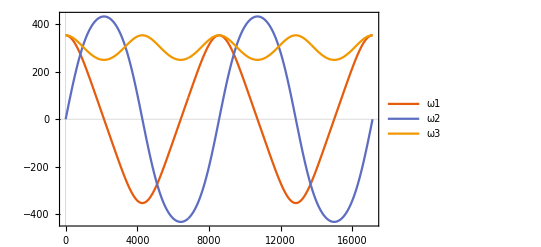

```mathematica
ω1=Transpose@{time,w1};
ω2=Transpose@{time,w2};
ω3=Transpose@{time,w3};
ListPlot[{ω1,ω2,ω3},Joined->True,PlotLegends->{"ω1","ω2","ω3"},PlotTheme->"Scientific"]
```

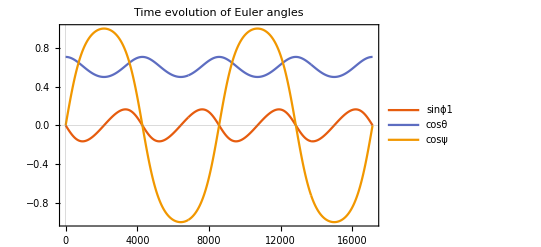

```mathematica
first1=Transpose@{time,sinϕ1};
first2=Transpose@{time,cosϕ2};
second=Transpose@{time,cosθ};
third=Transpose@{time,cosψ};
ListPlot[{first1,second,third},Joined->True, PlotLegends->{"sinϕ1","cosθ","cosψ"},PlotLabel->"Time evolution of Euler angles",PlotTheme->"Scientific",Axes->{True,False}]
```

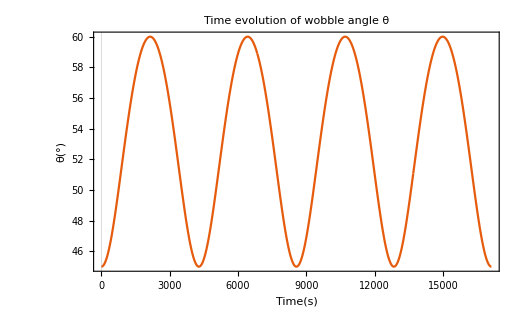

```mathematica
θ=ArcCos[Table[I3*b/J*JacobiDN[t*taut,k2],{t,0,n*T,dt}]]/π*180;
theta=Transpose@{time,θ};
ListPlot[theta,Joined->True,PlotTheme->"Scientific",PlotLabel->"Time evolution of wobble angle θ",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[θ[°]],None},{HoldForm[Time[s]],None}}]
```

Time evolution of θ̇, ψ̇ and ϕ̇

```mathematica
δ=1-1.0*√((I1(I3-I2))/(I2(I3-I1)));
dθ=Table[-1/J b I3 k2 taut JacobiCN[t taut,k2] JacobiSN[t taut,k2],{t,0,n*T,dt}]/(-sinθ);
dψ=Table[((-1+δ) JacobiDN[t*taut,k2])/((-1+δ)^2 JacobiCN[t*taut,k2]^2+JacobiSN[t*taut,k2]^2),{t,0,n*T,dt}];
dϕ=Re[Table[-1/T ⅈ π (EllipticThetaPrime[4,π ((2 t)/T-ⅈ α),q]/EllipticTheta[4,π ((2 t)/T-ⅈ α),q]-EllipticThetaPrime[4,π ((2 t)/T+ⅈ α),q]/EllipticTheta[4,π ((2 t)/T+ⅈ α),q]),{t,0,n*T,dt}]]+2π/T1;
```

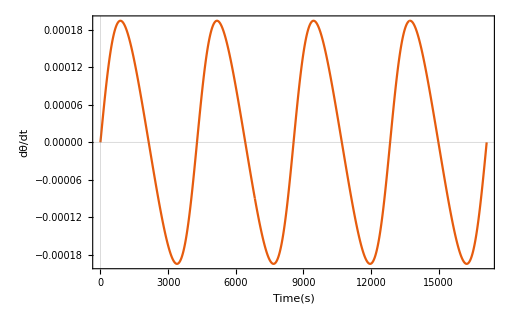

```mathematica
dtheta=Transpose@{time,dθ};
ListPlot[dtheta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dθ/dt],None},{HoldForm[Time[s]],None}}]
```

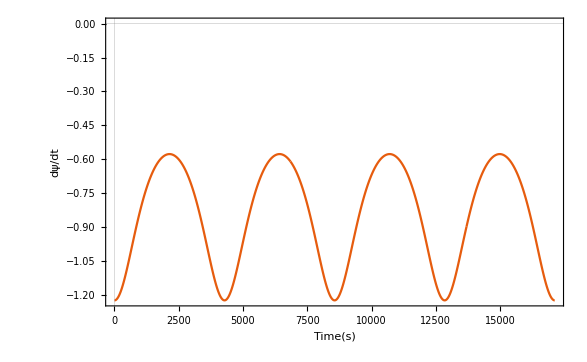

```mathematica
dpsi=Transpose@{time,dψ};
ListPlot[dpsi,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dψ/dt],None},{HoldForm[Time[s]],None}}]
```

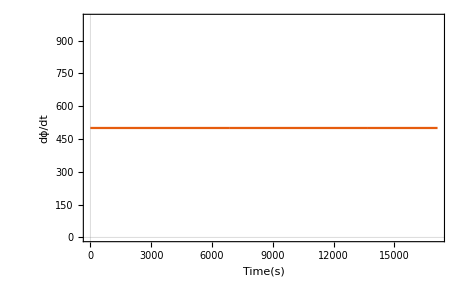

```mathematica
dphi=Transpose@{time,dϕ};
ListPlot[dphi,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[dϕ/dt],None},{HoldForm[Time[s]],None}}]
```

```mathematica
χ=0.2;
sinχ=Sin[χ];
cosχ=Cos[χ];
ΔP=((-cosψ sinχ (cosχ cosθ+sinχ sinθ sinψ) dθ+(cosψ^2 (sinχ)^2+(cosχ sinθ-cosθ sinχ sinψ)^2) dϕ+sinχ(cosθ sinχ-cosχ sinθ sinψ) dψ)/(cosψ^2 (sinχ)^2+(cosχ sinθ-cosθ sinχ sinψ)^2)-dϕ-dψ*(Sign[χ-θ]+1)/2)*T1^2/2.0/π;
```

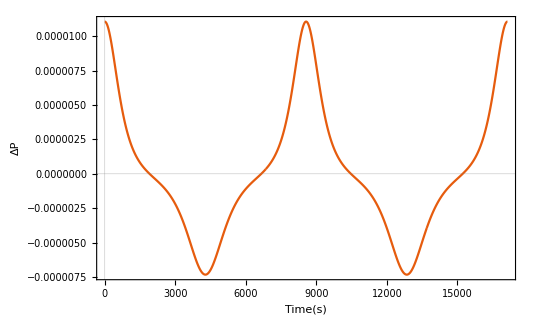

```mathematica
residual=Transpose@{time,ΔP};
ListPlot[residual,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[ΔP],None},{HoldForm[Time[s]],None}}]
```

The equivalent form of the pulse width is

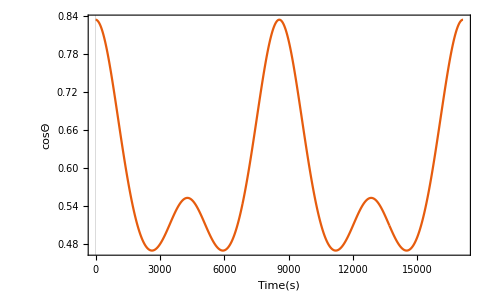

```mathematica
cosΘ=sinθ*sinψ*sinχ+ cosθ*cosχ;
CTheta=Transpose@{time,cosΘ};
ListPlot[CTheta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[cosΘ],None},{HoldForm[Time[s]],None}}]
```

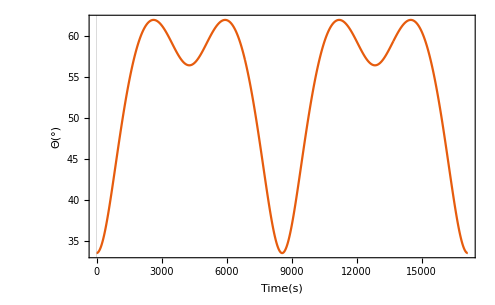

```mathematica
Θ=ArcCos[sinθ*sinψ*sinχ+ cosθ*cosχ];
Theta=Transpose@{time,Θ/π*180};
ListPlot[Theta,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[Θ [Degree]],None},{HoldForm[Time [s]],None}}]
```

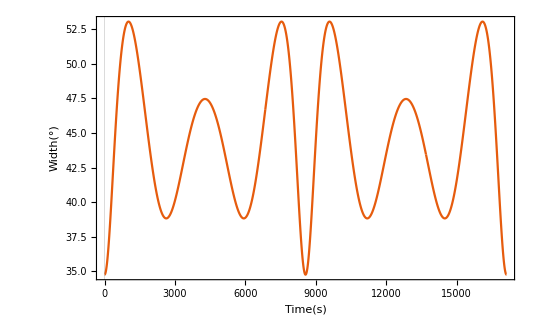

```mathematica
γ=50/180*π;
ρ=20/180*π;
W=ArcCos[(Cos[ρ]-Cos[Θ]Cos[γ])/(Sin[Θ]Sin[γ])]*2;
Width=Transpose@{time,W/π*180};
ListPlot[Width,Joined->True,PlotTheme->"Scientific",LabelStyle->{18,GrayLevel[0]},FrameLabel->{{HoldForm[Width [Degree]],None},{HoldForm[Time [s]],None}}]
```